# Beyond typology beyond optimization Part 2

## d) Qualitative evaluation

The code is structured as follows:
Cells in yellow are variables that need to be check, always run first 
Cells in red contain code to load data, always after the yellow cells
Cells in blue contain code, always run in order
Cells in white are to check the consistency of the data, not need to run

Run this cell first

Define the user name and the size of the SOM you want to load

```mathematica
somX=20;
somY=20;
user="Karla";
```

This part will take 30 seconds to run

```mathematica
indexListSorted=Import[NotebookDirectory[]<>"indexListSortedRe_"<>user<>".m"];
coordsSorted=Import[NotebookDirectory[]<>"coordsSortedRe_"<>user<>".m"];
somImage=First@Import[NotebookDirectory[]<>"som"<>ToString@somX<>ToString@somY<>"_"<>user<>"_SOM.pdf"];
cellQ=Import[NotebookDirectory[]<>"cell_quatityRe_"<>user<>".m"];
blueRed1=Import[NotebookDirectory[]<>"blueRed1_"<>user<>".m"];

edgeNode="edge_node_190613.csv";
edgesConnection=ImportEdgeConnection[edgeNode];
somImage
```

## Functions

```mathematica
ImportEdgeConnection[edgeNode_]:=
Block[{edgesConection},
edgesConection=Import[NotebookDirectory[]<>edgeNode];
edgesConection=1+#&/@#&/@edgesConection;
Return@edgesConection
]
```

```mathematica
FormFilter[cell1_,radius_]:=
Block[{g,selectedClusters,newList,sel,formsSelected},

g=GridGraph[{somX,somY},VertexSize->0.6];
selectedClusters=Join[AdjacencyList[g,cell1,radius],{cell1}];
newList=Flatten[indexListSorted[[selectedClusters]],1];
sel=Rotate[HighlightGraph[g,selectedClusters],270Degree];
formsSelected=Total[cellQ[[#]]&/@selectedClusters];

<|
"g"->g;
"newList"->newList,
"sel"->sel,
"formsSelected"->formsSelected
|>
]
```

```mathematica
Forms[id_]:=
Block[{cells,indexListSorted,coordsSorted,edgesConnection},

cells=Table[Graphics3D[
{Thickness[0.005],
blueRed1[[indexListSorted[[id,i]],#]],
Line[Partition[coordsSorted[[id,i]],3][[edgesConnection[[#]]]]]
}&/@Range@Length@edgesConnection,Boxed->False(*,ViewPoint->Top*)],{i,1,6}];

Grid[Partition[cells,3]]
]
```

## Selection

By running this line, you will be able to navigate in the SOM and select the cells to work with.

#### Load interface

Press + to open a slider so you can go up and down navigating around the SOM

```mathematica
(*somImage=ImageResize[somImage,ImageDimensions[somImage]/2];*)
imgDim=ImageDimensions[somImage];

cellSize=imgDim/{somX,somY};
Row[{Manipulate[
id=y*somX+x+1;
Show[{somImage,Graphics[{FaceForm[],EdgeForm[{Red,Thick}],Rectangle[{x,somY-y-1}*cellSize,{x+1,somY-y}*cellSize]},PlotRange-> {{0,imgDim[[1]]},{0,imgDim[[2]]}},PlotRangePadding->0,ImageSize->Medium]}]
,{x,0,somX-1,1},{y,0,somY-1,1},ContentSize->imgDim+20],Spacer[50],Style["cell N = ",Black,24],Dynamic[Style[id,Black,24]],Spacer[30],Dynamic[cells=Table[Graphics3D[
{Thickness[0.005],
blueRed1[[indexListSorted[[id,i]],#]],
Line[Partition[coordsSorted[[id,i]],3][[edgesConnection[[#]]]]]
}&/@Range@Length@edgesConnection,Boxed->False(*,ViewPoint->Top*)],{i,6}];

Grid[Partition[cells,3]]],Spacer[30],Style["forms in cell = ",Black,24],Dynamic[Style[cellQ[[id]],Black,24]]}]
```

#### List prefer and non-prefer design options

When you know the cell you want to select you can also select the neighboring cell by defining a radius taking all the forms contained in this range.

Forms 1 --- FormFilter[cell, radius]

Create two lists, start with formsPrefere when you finish the selection, export the list and continue with the new selection changing the name of the tag to formsNonPrefer

```mathematica
tag="formsPrefer"
```

formsNonPrefer

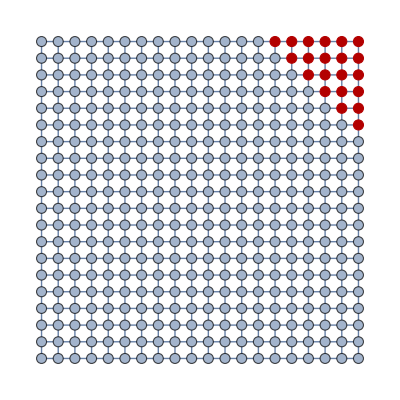

273 Selected

```mathematica
forms1=FormFilter[400,5];
forms1["sel"]

"Selected"   forms1["formsSelected"]
forms1=forms1["newList"];
```

Forms 2 --- FormFilter[cell, radius]

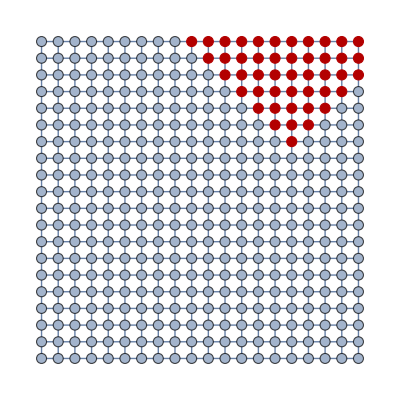

470 Selected

```mathematica
forms2=FormFilter[320,6];
forms2["sel"]

"Selected"   forms2["formsSelected"]
forms2=forms2["newList"];
```

Forms 3 --- FormFilter[cell, radius]

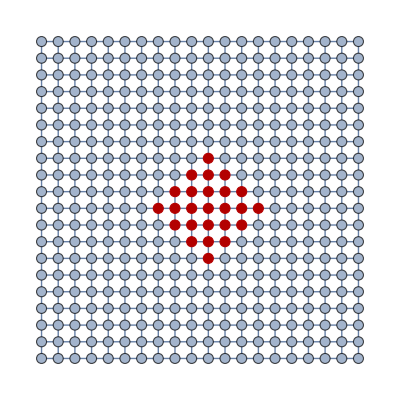

136 Selected

```mathematica
forms3=FormFilter[210,3];
forms3["sel"]

"Selected"   forms3["formsSelected"]
forms3=forms3["newList"];
```

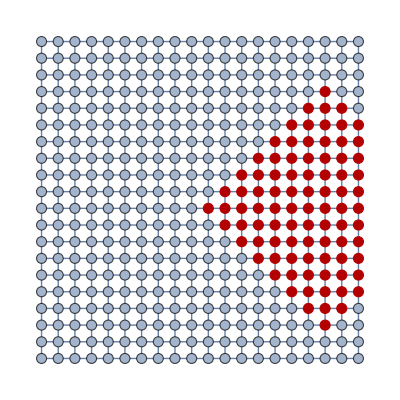

466 Selected

```mathematica
forms4=FormFilter[350,7];
forms4["sel"]

"Selected"   forms4["formsSelected"]
forms4=forms4["newList"];
```

```mathematica
Export[NotebookDirectory[]<>tag<>".m",Flatten[Join[{forms1,forms2,forms3,forms4}],1]];
```